```mathematica
yt[b_]=(1+b)/(2+b)
A[x_,b_]=yt[b]+(1+b)(x-1)+(1+b)Abs[x-yt[b]]
```

(1+b)/(2+b)

(1+b)/(2+b)+(1+b) (-1+x)+(1+b) Abs[-(1+b)/(2+b)+x]

```mathematica
Table[A[x,10],{x,0,1,1/20}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,11/15,11/6}

```mathematica
Plot3D[A[x,b],{x,0,1},{b,0,10},PlotRange->Full,AxesLabel->Automatic,MaxRecursion->7]
```

-Graphics3D-

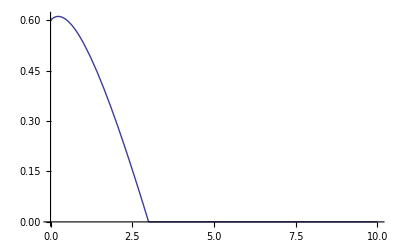

```mathematica
Plot[A[.8,b],{b,0,10},PlotRange->Full]
```

```mathematica
FullSimplify[A[x,b],Assumptions->x<yt[b]]
```

0

```mathematica
Clear[Ax]
Ax[x_]:=Maximize[{A[x,b],b≥0},b]
Ax[1/2]
Ax[9/10]//FullSimplify
```

{0,{b→84}}

{11/5-2 √(2/5),{b→-2+√10}}

```mathematica
FullSimplify[Ax[x],Assumptions->{0<x<1,x<yt[b]}]
FullSimplify[Ax[x],Assumptions->{0<x<1,x>yt[b]}]
```

{0,{b→84}}

Maximize[{(1+b)/(2+b)+(1+b) (-1+x)+(1+b) Abs[-(1+b)/(2+b)+x],b≥0},b]

```mathematica
FullSimplify[A[x,b],Assumptions->{0<x<1,x>yt[b]}]
Asub=Maximize[{FullSimplify[A[x,b],Assumptions->{0<x<1,x>yt[b]}],b≥0},b]
```

2 (1+b) (-1+1/(2+b)+x)

{Piecewise[{{1/2, x==3/4}, {2, x==1}, {-4 √(1-x)-2 (-2+x), 3/4<x<1}, {-1+2 x, x<3/4}, {∞, True}}],{b→Piecewise[{{0, x==3/4}, {(4-4 √(1-x)-2 (-2+x)-6 x)/(4 (-1+x))-1/4 √((8 (4 √(1-x)+2 (-2+x))+(4 √(1-x)+2 (-2+x))^2-4 (4 √(1-x)+2 (-2+x)) x+4 x^2)/(-1+x)^2), 3/4<x<1}, {(3-4 x)/(4 (-1+x))+1/4 √((8 (1-2 x)+(1-2 x)^2-4 (1-2 x) x+4 x^2)/(-1+x)^2), x<3/4}, {Indeterminate, True}}]}}

{∞,{b→Indeterminate}}

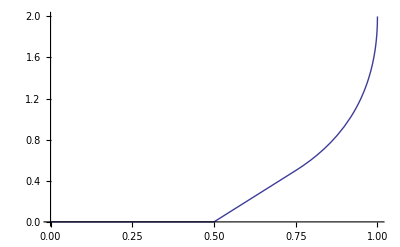

```mathematica
Plot[If[x<1/2,0,Asub[[1]]],{x,0,1}]
```

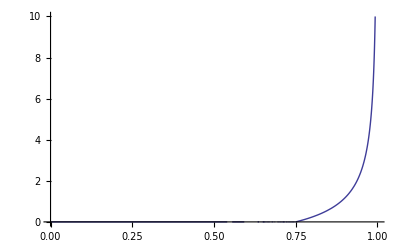

```mathematica
Plot[If[x<1/2,0,b/.Asub[[2]]],{x,0,1},PlotRange->{0,10}]
```

```mathematica
Integrate[Asub[[1]],{x,1/2,1}]
```

7/24

```mathematica
N[7/24]
```

0.291667

```mathematica
FullSimplify[D[A[x,b],b],Assumptions->x≥yt[b]]
```

Piecewise[{{2 (-1+1/(2+b)^2+x), 1/(2+b)+x>1}, {-(1+b)/(2+b)^2, True}}]

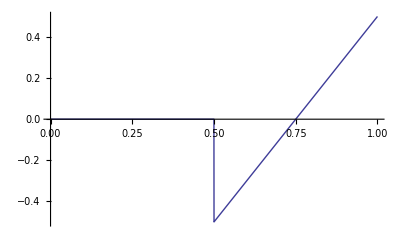

```mathematica
Plot[(A[x,10^-10]-A[x,0])/10^-10,{x,0,1}]
```

```mathematica
D[A[x,b],b]/.b->0
```

-3/4+x+Abs[-1/2+x]-1/4 Abs'[-1/2+x]

```mathematica
Plot[D[Abs[x],x],{x,-1,1}]
```

General::ivar: -0.999959 is not a valid variable.

General::ivar: -0.959143 is not a valid variable.

General::ivar: -0.918326 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
N[D[Abs[x],x]/.x->1]
```

Abs'[1.]

```mathematica
yt2[b_]=1-1/(1.9+b)
A2[x_,b_]=yt2[b]+(1+b)(x-1)+(1+b)Abs[x-yt2[b]]
NIntegrate[Max[0,Table[A2[x,b],{b,0,10,.01}]],{x,0,1}]
Plot3D[A2[x,b],{x,0,1},{b,0,10},PlotRange->Full,AxesLabel->Automatic,MaxRecursion->7]
```

1-1/(1.9+b)

1-1/(1.9+b)+(1+b) (-1+x)+(1+b) Abs[-1+1/(1.9+b)+x]

0.293681

-Graphics3D-

```mathematica
Integrate[A[x,2],{x,0,1}]
```

3/16

```mathematica
xt[b]=(2+2b+b^2)/(2+b)^2
```

(2+2 b+b^2)/(2+b)^2

```mathematica
Ab=Integrate[A[x,b],{x,xt[b],1},Assumptions->b>0]
```

(1+b)/(2+b)^2

```mathematica
Ab/.b->2
```

3/16

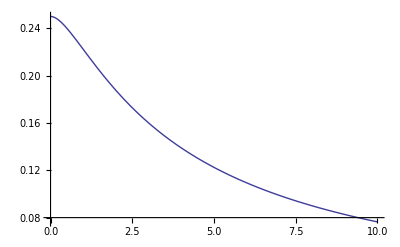

```mathematica
Plot[Ab,{b,0,10}]
```